## Тема I. 1^*

```mathematica
Clear[n]
RecurrenceTable[{p[n+1]==2^n √(2(1-√(1-(p[n]/2^n)^2))),p[2]==N[2 √2]},p,{n,3,60}]
```

{3.06147,3.12145,3.13655,3.14033,3.14128,3.14151,3.14157,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.1416,3.1416,3.14167,3.14183,3.14245,3.14245,3.16228,3.16228,3.4641,4.,8.,16.,32.,64.,128.,256.,512.,1024.,2048.,4096.,8192.,16384.,32768.,65536.,131072.,262144.,524288.,1.04858×10^6,2.09715×10^6,4.1943×10^6,8.38861×10^6,1.67772×10^7,3.35544×10^7,6.71089×10^7,1.34218×10^8,2.68435×10^8,5.36871×10^8,1.07374×10^9,2.14748×10^9,4.29497×10^9,8.58993×10^9}

```mathematica
Clear[n]
RecurrenceTable[{r[n+1]==r[n]/(2+√(4-r[n])),p[n+1]==2^n √(r[n]/(2+√(4-r[n]))),r[3]==N[2/(2+√2)],p[3]==N[2^2 √(2/(2+√2))]},{p,r},{n,3,60}]
```

{{3.06147,0.585786},{3.12145,0.152241},{3.13655,0.0384294},{3.14033,0.00963055},{3.14128,0.00240909},{3.14151,0.000602363},{3.14157,0.000150596},{3.14159,0.0000376494},{3.14159,9.41238×10^-6},{3.14159,2.3531×10^-6},{3.14159,5.88274×10^-7},{3.14159,1.47069×10^-7},{3.14159,3.67671×10^-8},{3.14159,9.19179×10^-9},{3.14159,2.29795×10^-9},{3.14159,5.74487×10^-10},{3.14159,1.43622×10^-10},{3.14159,3.59054×10^-11},{3.14159,8.97635×10^-12},{3.14159,2.24409×10^-12},{3.14159,5.61022×10^-13},{3.14159,1.40256×10^-13},{3.14159,3.50639×10^-14},{3.14159,8.76597×10^-15},{3.14159,2.19149×10^-15},{3.14159,5.47873×10^-16},{3.14159,1.36968×10^-16},{3.14159,3.42421×10^-17},{3.14159,8.56052×10^-18},{3.14159,2.14013×10^-18},{3.14159,5.35032×10^-19},{3.14159,1.33758×10^-19},{3.14159,3.34395×10^-20},{3.14159,8.35988×10^-21},{3.14159,2.08997×10^-21},{3.14159,5.22493×10^-22},{3.14159,1.30623×10^-22},{3.14159,3.26558×10^-23},{3.14159,8.16395×10^-24},{3.14159,2.04099×10^-24},{3.14159,5.10247×10^-25},{3.14159,1.27562×10^-25},{3.14159,3.18904×10^-26},{3.14159,7.9726×10^-27},{3.14159,1.99315×10^-27},{3.14159,4.98288×10^-28},{3.14159,1.24572×10^-28},{3.14159,3.1143×10^-29},{3.14159,7.78575×10^-30},{3.14159,1.94644×10^-30},{3.14159,4.86609×10^-31},{3.14159,1.21652×10^-31},{3.14159,3.04131×10^-32},{3.14159,7.60327×10^-33},{3.14159,1.90082×10^-33},{3.14159,4.75204×10^-34},{3.14159,1.18801×10^-34},{3.14159,2.97003×10^-35}}

## Тема II. 10.6 к

## Метод Гаусса

```mathematica
Clear[u];
n=10;
a[i_,j_,0]:=N[Piecewise[{{1, i== j}, {1/(i+j), i≠j}}]]
f[i_,0]:=N[1/i]
a[i_,j_,n_]:=a[i,j,n-1]+η[i,n]a[n,j,n-1]
f[i_,n_]:=f[i,n-1]+η[i,n]f[n,n-1]
η[i_,j_]:=-a[i,j,j-1]/a[j,j,j-1]
(*Array[Piecewise[{{a[#1,#2,#1-1], #2≥#1}, {0, #2<#1}}]&,{n,n}]//MatrixForm*)
u[n]=f[n,n-1]/a[n,n,n-1];
u[k_]:=u[k]=1/a[k,k,k-1](f[k,k-1]-∑_(i=k+1)^n a[k,i,k-1]u[i])
Array[u[#1]&,n]
Res=Array[f[#1,0]&,n]-Array[a[#1,#2,0]&,{n,n}].Array[u[#1]&,n](* невязка *)
VecNorm1[u_]:=Max[Abs[u]]
VecNorm2[u_]:=Total[Abs[u]]
VecNorm3[u_]:=u.u
VecNorm1[Res]
VecNorm2[Res]
VecNorm3[Res]
```

{0.919077,0.17554,0.0639348,0.0272748,0.0114235,0.00351084,-0.000789958,-0.0032508,-0.00469788,-0.00555374}

{2.22045×10^-16,0.,0.,5.55112×10^-17,2.77556×10^-17,0.,0.,1.38778×10^-17,1.38778×10^-17,-2.77556×10^-17}

2.22045×10^-16

3.60822×10^-16

5.43112×10^-32

## Метод Зейделя

```mathematica
AllTrue[λ/.Solve[Det[Array[Piecewise[{{λ a[#1,#2,0], #2≤ #1}, {a[#1,#2,0], #2>#1}}]&,{n,n}]]==0,λ],Abs[#]<1&](* Критерий сходимости*)
```

True

{0.919077,0.17554,0.0639348,0.0272748,0.0114235,0.00351084,-0.000789958,-0.0032508,-0.00469788,-0.00555374}

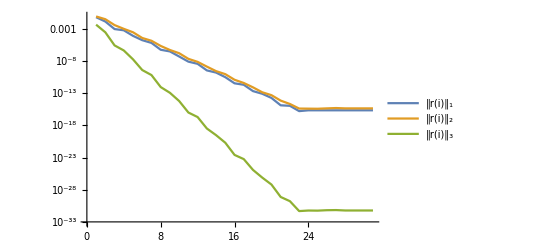

```mathematica
Clear[u,Res,i,n]
n=10;
L=Array[Piecewise[{{a[#1,#2,0], #1>#2}, {0, #1≤#2}}]&,{n,n}];
U=Array[Piecewise[{{a[#1,#2,0], #1<#2}, {0, #1≥#2}}]&,{n,n}];
DD=Array[Piecewise[{{a[#1,#2,0], #1==#2}, {0, #1≠#2}}]&,{n,n}];
R=-Inverse[L+DD].U;
F=Inverse[L+DD].Array[f[#1,0]&,n];
u[0]=Table[0,n];
u[k_]:=u[k]=R.u[k-1]+F
i=1;While[u[i]=!=u[i-1],i++] (* критерий остановки *)
u[i]
Res[k_]:=Array[f[#1,0]&,n]-Array[a[#1,#2,0]&,{n,n}].Array[u[k]⟦#⟧&,n](* невязка *)
ListLinePlot[{Table[VecNorm1[Res[k]],{k,i}],Table[VecNorm2[Res[k]],{k,i}],Table[VecNorm3[Res[k]],{k,i}]},ScalingFunctions->"Log",PlotLegends->{"‖r(i)‖_1","‖r(i)‖_2","‖r(i)‖_3"}]
```

## Нахождение λ_max и λ_min

```mathematica
Clear[u]
u[0]=Table[1,n];
A=Array[a[#1,#2,0]&,{n,n}];
u[k_]:=u[k]=Array[a[#1,#2,0]&,{n,n}].u[k-1];
 λMax[k_]:=(u[k+1].u[k])/(u[k].u[k]);
i=1;While[λMax[i]=!=λMax[i-1],i++]
AccurateλMax=λMax[i]
Clear[u]
u[0]=Table[1,n];
u[k_]:=u[k]=Inverse[A].u[k-1];
i=1;While[λMax[i]=!=λMax[i-1],i++]
AccuracteλMin=1/λMax[i]
```

2.04836

0.65796

## Числа обусловленности

```mathematica
Norm1=Max[Table[∑_(j=1)^n Abs[a[i,j,0]],{i,n}]];(* Norm2 = Norm1, т.к. A -- симметричная *)
μ1=Max[Table[∑_(j=1)^n Abs[a[i,j,0]],{i,n}]] Max[Table[∑_(j=1)^n Inverse[Array[a[#1,#2,0]&,{n,n}]]⟦i,j⟧,{i,n}]](* μ2 = μ1, т.к. A -- симметричная *)
Norm3=AccurateλMax(* т.к. A -- симметричная *);
μ3=AccurateλMax/AccuracteλMin
```

1.76164

3.1132

## Решение встроенными функциями

```mathematica
Solve[Array[a[#1,#2,0]&,{n,n}].Array[Subscript[x, #]&,n]==Array[f[#,0]&,n],Array[Subscript[x, #]&,n]]
Max[Eigenvalues[Array[a[#1,#2,0]&,{n,n}]]]
Min[Eigenvalues[Array[a[#1,#2,0]&,{n,n}]]]
```

{{x_1→0.919077,x_2→0.17554,x_3→0.0639348,x_4→0.0272748,x_5→0.0114235,x_6→0.00351084,x_7→-0.000789958,x_8→-0.0032508,x_9→-0.00469788,x_10→-0.00555374}}

2.04836

0.65796

## Тема III. 5.13 - 1, 3

## 1

```mathematica
Clear[n,i]
data={431,409,429,422,530,505,459,499,526,563,587,595,647,669,746,760,778,828,846,836,916,956,1014,1076,1134,1024};
n=Length[data]-1;
Subscript[x, i_] :=20+i
Subscript[y, i_]:=data⟦i+1⟧
```

```mathematica
a=N[((n+1)∑_(i=0)^n Subscript[x, i] Subscript[y, i]-∑_(i=0)^n Subscript[x, i] ∑_(i=0)^n Subscript[y, i])/((n+1)∑_(i=0)^n Subscript[x, i]^2-(∑_(i=0)^n Subscript[x, i])^2)]
b=N[(∑_(i=0)^n Subscript[y, i]∑_(i=0)^n Subscript[x, i]^2-∑_(i=0)^n Subscript[x, i] Subscript[y, i]∑_(i=0)^n Subscript[x, i])/((n+1)∑_(i=0)^n Subscript[x, i]^2-(∑_(i=0)^n Subscript[x, i])^2)]
```

28.7258

-234.166

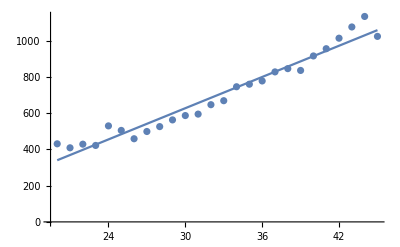

```mathematica
Show[ListPlot[{Table[Subscript[x, i],{i,0,n}],data}ᵀ],Plot[a x+b,{x,20,45}]]
```

```mathematica
∑_(i=0)^n (a Subscript[x, i]+b-Subscript[y, i])^2
```

56451.9

## 3

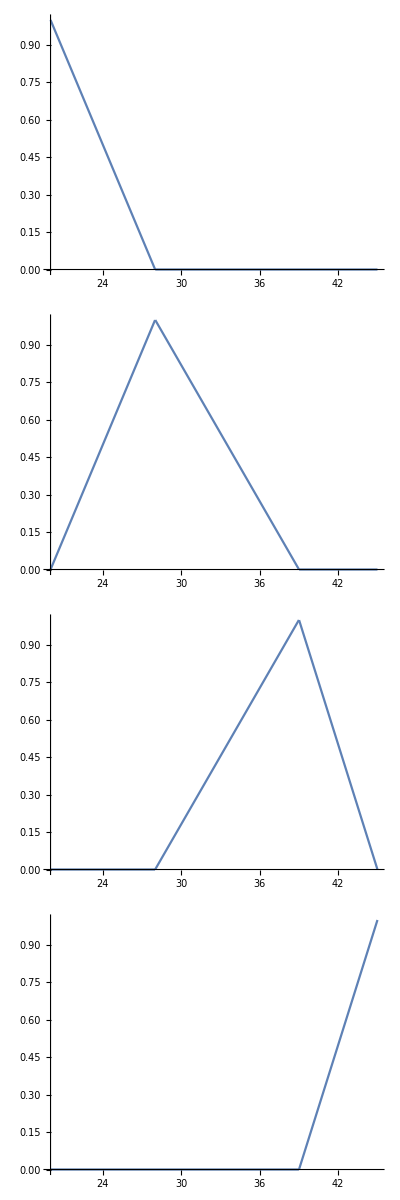

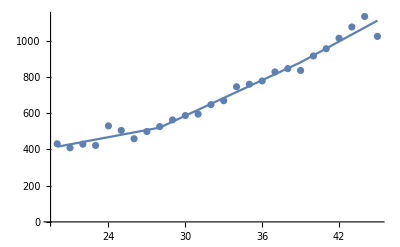

```mathematica
Clear[a]
Subscript[φ, 1][x_]:=Piecewise[{{(28-x)/8, 20≤x≤28}, {0, True}}]
Subscript[φ, 2][x_]:=Piecewise[{{(-20+x)/8, 20≤x≤28}, {(39-x)/11, 28≤x≤39}}]
Subscript[φ, 3][x_]:=Piecewise[{{(-28+x)/11, 28≤x≤39}, {(45-x)/6, 39≤x≤45}}]
Subscript[φ, 4][x_]:=Piecewise[{{(-39+x)/6, 39≤x≤45}, {0, True}}]
Column[Map[Plot[#,{x,20,45},PlotRange->All]&,Table[Subscript[φ, i][x],{i,4}]]]
⟨Subscript[φ, l_],Subscript[φ, k_]⟩:=∑_(i=0)^n Subscript[φ, l][Subscript[x, i]]Subscript[φ, k][Subscript[x, i]]
⟨Subscript[φ, l_],y⟩:=∑_(i=0)^n Subscript[φ, l][Subscript[x, i]] Subscript[y, i]
sol=Solve[N[Table[∑_(i=1)^4 ⟨Subscript[φ, j],Subscript[φ, i]⟩Subscript[a, i]==⟨Subscript[φ, j],y⟩,{j,4}]],Table[Subscript[a, i],{i,4}]];
Show[ListPlot[{Table[Subscript[x, i],{i,0,n}],data}ᵀ],Plot[∑_(i=1)^4 Subscript[a, i] Subscript[φ, i][x]/.sol,{x,20,45}]]
```

```mathematica
∑_(i=0)^n (∑_(j=1)^4 Subscript[a, j] Subscript[φ, j][Subscript[x, i]]-Subscript[y, i])^2/.sol
```

{25092.3}

значит данный метод лучше